```mathematica
data1=Import["/Users/yakimkina/_workspace/_mgtu/cpp/solving_interpolation_problems/output/fun1.10_Lagrange_nodes.csv",  {"CSV", "Data"}, "Numeric"->True];
data2=Import["/Users/yakimkina/_workspace/_mgtu/cpp/solving_interpolation_problems/output/fun1.10_Lagrange.csv", {"CSV", "Data"}, "Numeric"->True];
```

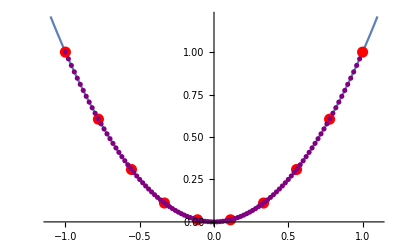

```mathematica
f = x^2;
p1 = Plot[f, {x, -1.1, 1.1}];
p2 = ListPlot[data1,PlotStyle->{Red, PointSize[0.02]}];
p3 = ListPlot[data2, PlotStyle-> {Purple}];
Show[p1, p2, p3]
```